```mathematica
repGen=Table[allGraphs6[k,"genfour"]->
Graph[allGraphs6[K6Key,"graph"],GraphHighlight->EdgeList[GraphComplement[allGraphs6[k,"graph"]]],VertexLabels->"Name",GraphHighlightStyle->"Thick",VertexStyle->Red,ImageSize->200]
,{k,gen6Sorted}];
```

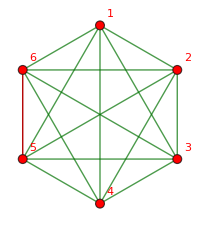
g1x2x3x4x56→-Graphics-

```mathematica
repGen[[2]]
```

```mathematica
Table[{allGraphs6[k,"graph"],Graph[FormulaGraph[allGraphs6[k,"colofour"]],ImageSize->600],TraditionalForm[allGraphs6[k,"genfour"]/.repGen]},{k,{lambdaKey}}];
```

```mathematica
repGen5=Table[allGraphs5[k,"genfour"]->
Graph[CompleteGraph[5],GraphHighlight->EdgeList[GraphComplement[allGraphs5[k,"graph"]]],VertexLabels->"Name",VertexStyle->Red,EdgeStyle->Blue,GraphHighlightStyle->{"Thick"},ImageSize->50]
,{k,gen5}];
```

```mathematica
repFull5=Table[allGraphs5[k,"colofour"]->
ShowGraph[allGraphs5,k]
,{k,allGraphs5AtomKeys}];
```

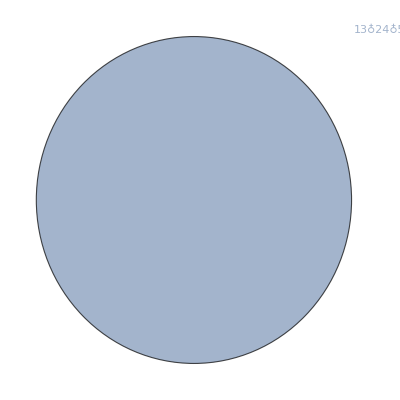
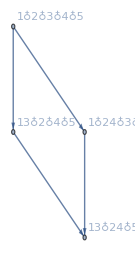
{{-Graphics-,-Graphics-,-Graphics-,-Graphics---Graphics---Graphics-+-Graphics-,-Graphics-36166}}

```mathematica
Table[{allGraphs5[k,"graph"],Graph[FormulaGraph[allGraphs5[k,"colofour"]],ImageSize->400],Graph[FormulaGraph[allGraphs5[k,"genfour"]],ImageSize->400],TraditionalForm[allGraphs5[k,"genfour"]/.repGen5],allGraphs5[k,"colofour"]/.repFull5},{k,{alfa1Key}}]
```

```mathematica
allGraphs5[29511,"parents"]
```

{29484,29430,29268,28782,27324,22950,9828}

```mathematica
allGraphs5[29484,"children"]
```

{{29511,29542},{29493,29502},{29487,29517},{29485,29513}}

```mathematica
,
```

```mathematica
repColor={Plus->Style["+",Red,50],Minus ->Style["-",50,Green]}
```

{Plus→+,Minus→-}

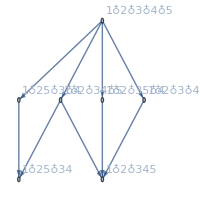
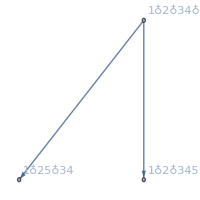
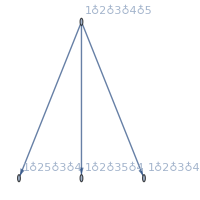
{{-Graphics-,-Graphics-v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,-Graphics-g1x25x34+g1x2x345-g1x2x34x5,--Graphics-+-Graphics-+-Graphics-,-Graphics-29560+-Graphics-29537+-Graphics-29533+-Graphics-29551+-Graphics-29525+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,-Graphics-g1x25x3x4+g1x2x35x4+g1x2x3x45-2 g1x2x3x4x5,-2 -Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-29551+-Graphics-29525+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-v1x25x34+v1x2x345+v1x2x34x5,-Graphics-g1x25x34-g1x25x3x4+g1x2x345-g1x2x34x5-g1x2x35x4-g1x2x3x45+2 g1x2x3x4x5,2 -Graphics---Graphics---Graphics---Graphics---Graphics-+-Graphics-+-Graphics-,-Graphics-29560+-Graphics-29537+-Graphics-29533}}

```mathematica
Table[{allGraphs5[k,"graph"],Labeled[Graph[FormulaGraph[allGraphs5[k,"colofour"]],ImageSize->{200,200}],allGraphs5[k,"colofour"]],Labeled[Graph[FormulaGraph[allGraphs5[k,"genfour"]],ImageSize->{200,200}],allGraphs5[k,"genfour"]],TraditionalForm[allGraphs5[k,"genfour"]/.repGen5],allGraphs5[k,"colofour"]/.repFull5},{k,{29484,29493,29502}}]
```

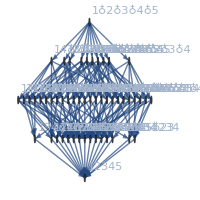
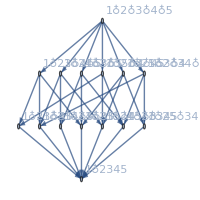
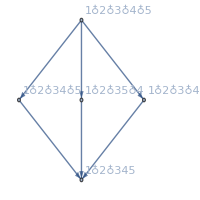
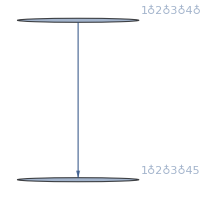
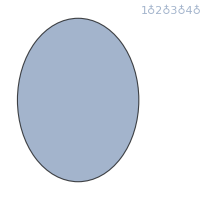
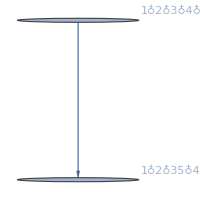
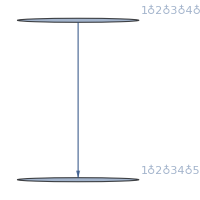
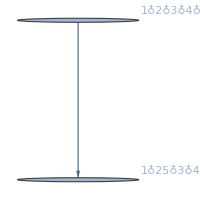
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-59048+-Graphics-58288+-Graphics-56770+-Graphics-56012+-Graphics-52232+-Graphics-49972+-Graphics-49220+-Graphics-51478+-Graphics-39014+-Graphics-32684+-Graphics-30586+-Graphics-29888+-Graphics-31984+-Graphics-36898+-Graphics-36194+-Graphics-38308+-Graphics-56011+-Graphics-51475+-Graphics-49216+-Graphics-49963+-Graphics-49210+-Graphics-49208+-Graphics-38281+-Graphics-31954+-Graphics-29857+-Graphics-36166+-Graphics-36817+-Graphics-30496+-Graphics-29797+-Graphics-36112+-Graphics-36086+-Graphics-29768+-Graphics-32441+-Graphics-30334+-Graphics-29633+-Graphics-31738+-Graphics-30262+-Graphics-29560+-Graphics-29537+-Graphics-31714+-Graphics-29608+-Graphics-49207+-Graphics-36085+-Graphics-29767+-Graphics-31711+-Graphics-29605+-Graphics-29533+-Graphics-30253+-Graphics-29551+-Graphics-29525+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29888+-Graphics-29857+-Graphics-29797+-Graphics-29768+-Graphics-29633+-Graphics-29560+-Graphics-29537+-Graphics-29608+-Graphics-29767+-Graphics-29605+-Graphics-29533+-Graphics-29551+-Graphics-29525+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29537+-Graphics-29533+-Graphics-29525+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29525+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29533+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29551+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29560+-Graphics-29533+-Graphics-29551+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29605+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29608+-Graphics-29605+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29633+-Graphics-29605+-Graphics-29551+-Graphics-29525+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29768+-Graphics-29767+-Graphics-29525+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29767+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29797+-Graphics-29767+-Graphics-29551+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-29857+-Graphics-29767+-Graphics-29605+-Graphics-29533+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-30253+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-30262+-Graphics-29533+-Graphics-30253+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-30334+-Graphics-29605+-Graphics-30253+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-30496+-Graphics-29767+-Graphics-30253+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-30586+-Graphics-29857+-Graphics-30496+-Graphics-30334+-Graphics-30262+-Graphics-29767+-Graphics-29605+-Graphics-29533+-Graphics-30253+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-31711+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-31714+-Graphics-31711+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-31738+-Graphics-31711+-Graphics-29551+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-31954+-Graphics-29767+-Graphics-31711+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-31984+-Graphics-31954+-Graphics-29797+-Graphics-31738+-Graphics-31714+-Graphics-29767+-Graphics-31711+-Graphics-29551+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-32441+-Graphics-31711+-Graphics-30253+-Graphics-29525+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-32684+-Graphics-31954+-Graphics-30496+-Graphics-29768+-Graphics-32441+-Graphics-29767+-Graphics-31711+-Graphics-30253+-Graphics-29525+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-36086+-Graphics-36085+-Graphics-29525+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-36085+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-36112+-Graphics-36085+-Graphics-29551+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-36166+-Graphics-36085+-Graphics-29605+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-36194+-Graphics-36166+-Graphics-36112+-Graphics-36086+-Graphics-29633+-Graphics-36085+-Graphics-29605+-Graphics-29551+-Graphics-29525+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-36817+-Graphics-36085+-Graphics-30253+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-36898+-Graphics-36166+-Graphics-36817+-Graphics-30334+-Graphics-29608+-Graphics-36085+-Graphics-29605+-Graphics-30253+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-38281+-Graphics-36085+-Graphics-31711+-Graphics-29533+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-38308+-Graphics-38281+-Graphics-36112+-Graphics-31738+-Graphics-29560+-Graphics-36085+-Graphics-31711+-Graphics-29533+-Graphics-29551+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-39014+-Graphics-38281+-Graphics-36817+-Graphics-36086+-Graphics-32441+-Graphics-30262+-Graphics-29537+-Graphics-31714+-Graphics-36085+-Graphics-31711+-Graphics-29533+-Graphics-30253+-Graphics-29525+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-49220+-Graphics-49216+-Graphics-49210+-Graphics-49208+-Graphics-29537+-Graphics-49207+-Graphics-29533+-Graphics-29525+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-49208+-Graphics-49207+-Graphics-29525+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-49207+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-49210+-Graphics-49207+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-49216+-Graphics-49207+-Graphics-29533+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-49963+-Graphics-49207+-Graphics-30253+-Graphics-29551+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-49972+-Graphics-49216+-Graphics-49963+-Graphics-30262+-Graphics-29560+-Graphics-49207+-Graphics-29533+-Graphics-30253+-Graphics-29551+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-51475+-Graphics-49207+-Graphics-31711+-Graphics-29605+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-51478+-Graphics-51475+-Graphics-49210+-Graphics-31714+-Graphics-29608+-Graphics-49207+-Graphics-31711+-Graphics-29605+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-52232+-Graphics-51475+-Graphics-49963+-Graphics-49208+-Graphics-32441+-Graphics-30334+-Graphics-29633+-Graphics-31738+-Graphics-49207+-Graphics-31711+-Graphics-29605+-Graphics-30253+-Graphics-29551+-Graphics-29525+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-56012+-Graphics-56011+-Graphics-49208+-Graphics-36086+-Graphics-29768+-Graphics-49207+-Graphics-36085+-Graphics-29767+-Graphics-29525+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-56011+-Graphics-49207+-Graphics-36085+-Graphics-29767+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-56770+-Graphics-56011+-Graphics-49963+-Graphics-49210+-Graphics-36817+-Graphics-30496+-Graphics-29797+-Graphics-36112+-Graphics-49207+-Graphics-36085+-Graphics-29767+-Graphics-30253+-Graphics-29551+-Graphics-29527+-Graphics-29524},{-Graphics-,-Graphics-,-Graphics-,-Graphics-58288+-Graphics-56011+-Graphics-51475+-Graphics-49216+-Graphics-38281+-Graphics-31954+-Graphics-29857+-Graphics-36166+-Graphics-49207+-Graphics-36085+-Graphics-29767+-Graphics-31711+-Graphics-29605+-Graphics-29533+-Graphics-29524}}

```mathematica
Table[{allGraphs5[k,"graph"],Graph[FormulaGraph[allGraphs5[k,"colofour"]],ImageSize->{200,200}],TraditionalForm[allGraphs5[k,"genfour"]/.repGen5],allGraphs5[k,"colofour"]/.repFull5},{k,gen5}]
```